```mathematica
fair = {1,0,1,0,0,1};
efficiency = {0,0,1,0,0,0}; 
selfish = {0,1,1,1,1,1}
```

```mathematica
Error[w1_,w2_,w3_]:=Module[{guess},
guess =w1*fair + w2*efficiency + w3*selfish;
Total[(guess-actual)^2]]
```

```mathematica
sol=NMinimize[{Error[w1,w2,w3],w1>=0 && w1<=1 && w2>=0&& w2<= 1&&w3>=0 && w3 <= 1 && w1 + w2 +w3==1},{w1,w2,w3}]
```

{0.200643,{w1→0.154286,w2→0.324286,w3→0.521429}}

```mathematica
guess = w1*fair + w2*efficiency + w3*selfish/.Last[sol]
actual = {0.31, 0.78, 1, 0.27, 0.67, 0.52}
```

```mathematica
?BarChart
```

```mathematica
labels = {"Berk29", "Berk26", "Berk23", "Berk15", "Barc8", "Barc2"}
```

{Berk29,Berk26,Berk23,Berk15,Barc8,Barc2}

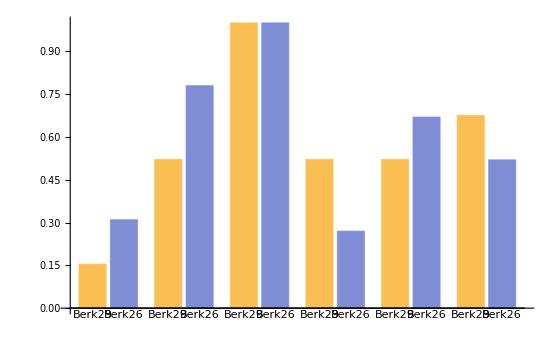

```mathematica
BarChart[Transpose[{guess,actual}],ChartLabels->labels]
```